## Nutrient-Dependent extension of Mumby et al. (2007) model x_1 = macroalgae; x_2 = coral; x_3 = algal turf

```mathematica
Clear[f1,f2,x1,x2,x3]
```

```mathematica
f1= a (Nt/(N0+Nt)) x1 x2 - (g x1)/(x1+ x3) + y x1 x3;
```

```mathematica
f2=x2 (r(1-cal Nt) x3- m -a (Nt/(N0+Nt)) x1) ;

x3=1 - x1- x2 ;
```

```mathematica
reef[{M0_,C0_}]:=Module[{transform={x1->x1[t],x2->x2[t]}},
{x1'[t]==(f1/.transform),
x2'[t]==(f2/.transform),
x1[0]==M0,
x2[0]==C0}
]
```

Set mutable list of default parameters

```mathematica
Clear[param]
```

```mathematica
param=Dispatch[{
a->2.3,      
g->0.4,
y->0.7,
r -> 1.8,
m->0.15,
N0->0.5,
Nt->0.5,
cal->0.25
}]
```

### Model Isoclines

```mathematica
FullSimplify[Solve[f1==0,x1]]
```

```mathematica
FullSimplify[Solve[f2==0,x1]]
```

#### Plot Isoclines - vary parameters as needed for Figure 2a and SA.2

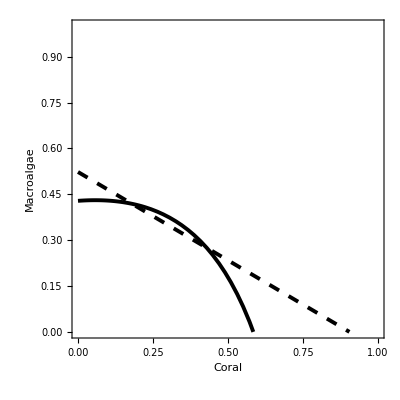

```mathematica
Plot[{X1=(g/(-1+X2)+(a Nt X2)/(N0+Nt)+y-X2 y)/y/.param,X1=((N0+Nt) (m-(-1+cal Nt) r (-1+X2)))/(-a Nt+(N0+Nt) (-1+cal Nt) r)/.param },  {X2, 0, 1.0},PlotRange->{{0.0,1.0},{0.0,1.0}},FrameLabel->{Style["Coral",FontSize->14,Bold],Style["Macroalgae",FontSize->14,Bold]},PlotStyle->{{Black,Thickness[0.007]},{Black,Dashing[0.02],Thickness[0.007]}},Frame->True, Axes -> True,AspectRatio->1,ImageSize->400]
```

### Create ODE solver and add possibility of perturbations

```mathematica
tmax=5000
```

5000

```mathematica
Clear[sol]
```

```mathematica
sol[M0_,C0_,spar_,freq_,szC_,szM_]:=NDSolve[{reef[{M0,C0}]/.spar/.param,perturb[freq,szC,szM]},{x1,x2},{t,0,tmax},AccuracyGoal->40,MaxStepSize->0.01,MaxSteps->10^6,Method->{"StiffnessSwitching"}];
```

## Figures

### Figure 2b

Count number of interior equilibria to find areas of bistability in parameter space (grazing and nutrient loading)

```mathematica
Clear[findIntEqs]
findIntEqs[spar_]:=Module[{eqs},
eqs=NSolve[{f1==0,f2==0}/.spar/.param,{x1,x2}];
Select[eqs,And@@Positive[#[[All,2]]]&]
]
```

(decrease step size between parameter values in function for higher resolution)

```mathematica
NumIntEqs=Flatten[Table[Join[{nut,gval,Length[findIntEqs[{Nt->nut,g->gval}]]}],{nut,0.0,4.0,0.05},{gval,0.0,1.0,0.01}],1];
```

```mathematica
ListDensityPlot[NumIntEqs,FrameLabel->{Style["Nutrients",FontSize->14,Bold],Style["Grazing",FontSize->14,Bold]},ColorFunction->"GrayTones"]
```

### Figure 3

Phase plane figures with isoclines and trajectories (Fig 3a)

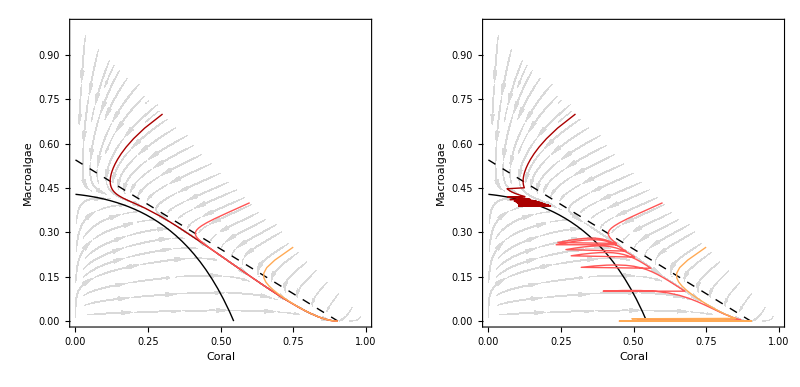

```mathematica
GraphicsRow[{
Show[{
StreamPlot[Evaluate[{f2,f1}/.g->0.4/.Nt->0.53/.a->2/.param],{x2,0.0,1.0},{x1,0.0,1.0},FrameLabel->{Style["Coral",FontSize->16,Bold],Style["Macroalgae",FontSize->16,Bold]},StreamScale->Large, PlotRange->{{0.0,1.0},{0.0,1.0}},StreamColorFunction->None,StreamStyle->{LightGray,"PinDart"},RegionFunction->Function[{x1,x2},x1+x2<1],RegionBoundaryStyle->None,RegionFillingStyle->None,Frame->True, Axes -> True,AspectRatio->1],
Plot[{X1=(g/(-1+X2)+(a Nt X2)/(N0+Nt)+y-X2 y)/y/.g->0.4/.a->2/.Nt->0.53/.param,X1=((N0+Nt) (m-(-1+cal Nt) r (-1+X2)))/(-a Nt+(N0+Nt) (-1+cal Nt) r)/.a->2/.Nt-> 0.53/.param },  {X2, 0, 1.0},PlotRange->{{0.0,1.0},{0.0,1.0}},PlotStyle->{{Black,Thick},{Black,Dashing[0.02],Thick}}],
ParametricPlot[Evaluate[{x2[t],x1[t]}/.sol[0.7,0.3,{a->2,g->0.4,Nt->0.53},5,0.0,0.0]],{t,0,1000},PlotRange->{{0.0,1.0},{0.0,1.0}},PlotStyle->{Darker[Red],Thick},Frame->True, Axes -> True],
ParametricPlot[Evaluate[{x2[t],x1[t]}/.sol[0.4,0.6,{a->2,g->0.4,Nt->0.53},5,0.0,0.0]],{t,0,1000},PlotRange->{{0.0,1.0},{0.0,1.0}},PlotStyle->{Lighter[Red],Thick},Frame->True, Axes -> True],
ParametricPlot[Evaluate[{x2[t],x1[t]}/.sol[0.25,0.75,{a->2,g->0.4,Nt->0.53},5,0.0,0.0]],{t,0,1000},PlotRange->{{0.0,1.0},{0.0,1.0}},PlotStyle->{Lighter[Orange],Thick},Frame->True, Axes -> True]},ImageSize->300],
Show[{
StreamPlot[Evaluate[{f2,f1}/.g->0.4/.Nt->0.53/.a->2/.param],{x2,0.0,1.0},{x1,0.0,1.0},FrameLabel->{Style["Coral",FontSize->16,Bold],Style["Macroalgae",FontSize->16,Bold]},StreamScale->Large, PlotRange->{{0.0,1.0},{0.0,1.0}},StreamColorFunction->None,StreamStyle->{LightGray,"PinDart"},RegionFunction->Function[{x1,x2},x1+x2<1],RegionBoundaryStyle->None,RegionFillingStyle->None,Frame->True, Axes -> True,AspectRatio->1],
Plot[{X1=(g/(-1+X2)+(a Nt X2)/(N0+Nt)+y-X2 y)/y/.g->0.4/.a->2/.Nt->0.53/.param,X1=((N0+Nt) (m-(-1+cal Nt) r (-1+X2)))/(-a Nt+(N0+Nt) (-1+cal Nt) r)/.a->2/.Nt-> 0.53/.param },  {X2, 0, 1.0},PlotRange->{{0.0,1.0},{0.0,1.0}},PlotStyle->{{Black,Thick},{Black,Dashing[0.02],Thick}}],
ParametricPlot[Evaluate[{x2[t],x1[t]}/.sol[0.7,0.3,{a->2,g->0.4,Nt->0.53},5,0.5,0.0]],{t,0,1000},PlotRange->{{0.0,1.0},{0.0,1.0}},PlotStyle->{Darker[Red],Thick},Frame->True, Axes -> True],
ParametricPlot[Evaluate[{x2[t],x1[t]}/.sol[0.4,0.6,{a->2,g->0.4,Nt->0.53},5,0.5,0.0]],{t,0,1000},PlotRange->{{0.0,1.0},{0.0,1.0}},PlotStyle->{Lighter[Red],Thick},Frame->True, Axes -> True],
ParametricPlot[Evaluate[{x2[t],x1[t]}/.sol[0.25,0.75,{a->2,g->0.4,Nt->0.53},5,0.5,0.0]],{t,0,1000},PlotRange->{{0.0,1.0},{0.0,1.0}},PlotStyle->{Lighter[Orange],Thick},Frame->True, Axes -> True]},ImageSize->300]},
ImageSize->800]
```

Time series corresponding to trajectory 3

```mathematica
GraphicsColumn[{Plot[Evaluate[{x1[t],x2[t],(1-x1[t]-x2[t])}/.sol[0.7,0.3,{a->2,g->0.4,Nt->0.53},5,0.0,0.0]],{t,0,100},FrameLabel->{Style["Time",FontSize->18,Bold],Style["Densities",FontSize->18,Bold]},Frame->True,Axes->False,PlotStyle->{Darker[Green],Pink,Lighter[Gray]},PlotRange->{All,{0,1.0}},PlotLegends->{"Macroalgae","Coral","Benthic r-strategists"},ImageSize->300],
Plot[Evaluate[{x1[t],x2[t],(1-x1[t]-x2[t])}/.sol[0.7,0.3,{a->2,g->0.4,Nt->0.53},5,0.5,0.0]],{t,0,100},FrameLabel->{Style["Time",FontSize->18,Bold],Style["Densities",FontSize->18,Bold]},Frame->True,Axes->False,PlotStyle->{Darker[Green],Pink,Lighter[Gray]},PlotRange->{All,{0,1.0}},PlotLegends->{"Macroalgae","Coral","Benthic r-strategists"},ImageSize->300]},
ImageSize->600]
```

-Graphics-

### Figure 4

```mathematica
GraphicsGrid[{{
StackedListPlot[{
Flatten[x1[Range[0,100,1]]/.sol[0.5,0.5,{a->2.4,g->0.24,Nt->0.16},5,0,0.0]],
Flatten[x2[Range[0,100,1]]/.sol[0.5,0.5,{a->2.4,g->0.24,Nt->0.16},5,0,0.0]],
Flatten[0.24*(1-x1[Range[0,100,1]]-x2[Range[0,100,1]])/.sol[0.5,0.5,{a->2.4,g->0.24,Nt->0.16},5,0,0.0]],Flatten[0.76*(1-x1[Range[0,100,1]]-x2[Range[0,100,1]])/.sol[0.5,0.5,{a->2.4,g->0.24,Nt->0.16},5,0,0.0]]
},PlotStyle->{Darker[Green],Pink,Brown,Lighter[Green]},PlotLegends->{"Macroalgae","Coral","Less Palatable","Palatable"},Frame->True,FrameLabel->{Style["Time",FontSize->18,Bold],Style["Densities",FontSize->18,Bold]},ImageSize->350],
StackedListPlot[{
Flatten[x1[Range[0,100,1]]/.sol[0.5,0.5,{a->2.4,g->0.7,Nt->2.31},5,0,0.0]],
Flatten[x2[Range[0,100,1]]/.sol[0.5,0.5,{a->2.4,g->0.7,Nt->2.31},5,0,0.0]],
Flatten[0.7*(1-x1[Range[0,100,1]]-x2[Range[0,100,1]])/.sol[0.5,0.5,{a->2.4,g->0.7,Nt->2.31},5,0,0.0]],Flatten[0.3*(1-x1[Range[0,100,1]]-x2[Range[0,100,1]])/.sol[0.5,0.5,{a->2.4,g->0.7,Nt->2.31},5,0,0.0]]
},PlotStyle->{Darker[Green],Pink,Brown,Lighter[Green]},PlotLegends->{"Macroalgae","Coral","Less Palatable","Palatable"},Frame->True,FrameLabel->{Style["Time",FontSize->18,Bold],Style["Densities",FontSize->18,Bold]},ImageSize->350]
},{
StackedListPlot[{
Flatten[x1[Range[0,100,1]]/.sol[0.5,0.5,{a->2.4,g->0.24,Nt->0.16},5,0.5,0.0]],
Flatten[x2[Range[0,100,1]]/.sol[0.5,0.5,{a->2.4,g->0.24,Nt->0.16},5,0.5,0.0]],
Flatten[0.24*(1-x1[Range[0,100,1]]-x2[Range[0,100,1]])/.sol[0.5,0.5,{a->2.4,g->0.24,Nt->0.16},5,0.5,0.0]],Flatten[0.76*(1-x1[Range[0,100,1]]-x2[Range[0,100,1]])/.sol[0.5,0.5,{a->2.4,g->0.24,Nt->0.16},5,0.5,0.0]]
},PlotStyle->{Darker[Green],Pink,Brown,Lighter[Green]},PlotLegends->{"Macroalgae","Coral","Less Palatable","Palatable"},Frame->True,FrameLabel->{Style["Time",FontSize->18,Bold],Style["Densities",FontSize->18,Bold]},ImageSize->350],
StackedListPlot[{
Flatten[x1[Range[0,100,1]]/.sol[0.5,0.5,{a->2.4,g->0.7,Nt->2.31},5,0.5,0.0]],
Flatten[x2[Range[0,100,1]]/.sol[0.5,0.5,{a->2.4,g->0.7,Nt->2.31},5,0.5,0.0]],
Flatten[0.7*(1-x1[Range[0,100,1]]-x2[Range[0,100,1]])/.sol[0.5,0.5,{a->2.4,g->0.7,Nt->2.31},5,0.5,0.0]],Flatten[0.3*(1-x1[Range[0,100,1]]-x2[Range[0,100,1]])/.sol[0.5,0.5,{a->2.4,g->0.7,Nt->2.31},5,0.5,0.0]]
},PlotStyle->{Darker[Green],Pink,Brown,Lighter[Green]},PlotLegends->{"Macroalgae","Coral","Less Palatable","Palatable"},Frame->True,FrameLabel->{Style["Time",FontSize->18,Bold],Style["Densities",FontSize->18,Bold]},ImageSize->350]
}},ImageSize->1000]
```

-Graphics-

## Supplement A

#### Fig SA.3

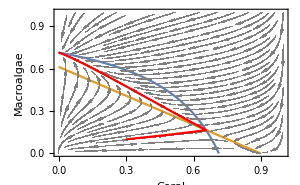

```mathematica
GraphicsRow[{
Show[{
Plot[{X1=(g/(-1+X2)+(a Nt X2)/(N0+Nt)+y-X2 y)/y/.g->0.2/.a->1.2/.Nt->0.69/.param,X1=((N0+Nt) (m-(-1+cal Nt) r (-1+X2)))/(-a Nt+(N0+Nt) (-1+cal Nt) r)/.a->1.2/.Nt-> 0.69/.param },  {X2, 0, 1.0},PlotRange->{{0.0,1.0},{0.0,1.0}},FrameLabel->{Style["Coral",FontSize->14,Bold],Style["Macroalgae",FontSize->14,Bold]},Frame->True, Axes -> True],
StreamPlot[Evaluate[{f2,f1}/.g->0.2/.Nt->0.69/.a->1.2/.param],{x2,0.0,1.0},{x1,0.0,1.0},FrameLabel->{Style["Coral",FontSize->14,Bold],Style["Macroalgae",FontSize->14,Bold]},StreamScale->Large, StreamColorFunction->None,StreamStyle->{Gray,"PinDart"}],
ParametricPlot[Evaluate[{x2[t],x1[t]}/.sol[0.1,0.3,{a->1.2,g->0.2,Nt->0.69},5,0,0.0]],{t,0,100},PlotRange->{{0.0,1.0},{0.0,1.0}},PlotStyle->Red,FrameLabel->{Style["Coral",FontSize->14,Bold],Style["Macroalgae",FontSize->14,Bold]},Frame->True, Axes -> True]},ImageSize->300],

Plot[Evaluate[{x1[t],x2[t]}/.sol[0.1,0.3,{a->1.2,g->0.2,Nt->0.69},5,0,0.0]],{t,0,100},FrameLabel->{Style["Time",FontSize->18,Bold],Style["Densities",FontSize->18,Bold]},Frame->True,Axes->False,PlotStyle->{Darker[Green],Pink},PlotRange->{All,{0,1}},PlotLegends->{"Macroalgae","Coral"},ImageSize->300]

},ImageSize->800]
```

#### Fig SA.4

```mathematica
GraphicsColumn[{Plot[Evaluate[{x1[t],x2[t],(1-x1[t]-x2[t])}/.sol[0.6,0.35,{a->2,g->0.41,Nt->0.55},5,0.0,0.0]],{t,0,800},FrameLabel->{Style["Time",FontSize->18,Bold],Style["Densities",FontSize->18,Bold]},Frame->True,Axes->False,PlotStyle->{Darker[Green],Pink,Lighter[Gray]},PlotRange->{All,{0,1.0}},PlotLegends->{"Macroalgae","Coral","Other"},ImageSize->350], Plot[Evaluate[{x1[t],x2[t],(1-x1[t]-x2[t])}/.sol[0.6,0.35,{a->2,g->0.41,Nt->0.55},5,0.47,0.0]],{t,0,800},FrameLabel->{Style["Time",FontSize->18,Bold],Style["Densities",FontSize->18,Bold]},Frame->True,Axes->False,PlotStyle->{Darker[Green],Pink,Lighter[Gray]},PlotRange->{All,{0,1.0}},PlotLegends->{"Macroalgae","Coral","Other"},ImageSize->350]},
ImageSize->600]
```

-Graphics-

#### Fig SA.5

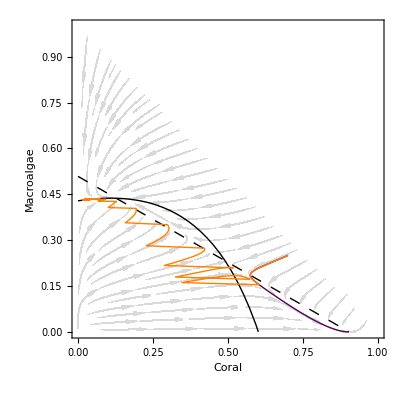

```mathematica
Show[{
StreamPlot[Evaluate[{f2,f1}/.Nt->0.55/.param],{x2,0.0,1.0},{x1,0.0,1.0},FrameLabel->{Style["Coral",FontSize->16,Bold],Style["Macroalgae",FontSize->16,Bold]},StreamScale->Large, PlotRange->{{0.0,1.0},{0.0,1.0}},StreamColorFunction->None,StreamStyle->{LightGray,"PinDart"},RegionFunction->Function[{x1,x2},x1+x2<1],RegionBoundaryStyle->None,RegionFillingStyle->None,Frame->True, Axes -> True,AspectRatio->1],
Plot[{X1=(g/(-1+X2)+(a Nt X2)/(N0+Nt)+y-X2 y)/y/.Nt->0.55/.param,X1=((N0+Nt) (m-(-1+cal Nt) r (-1+X2)))/(-a Nt+(N0+Nt) (-1+cal Nt) r)/.Nt-> 0.55/.param },  {X2, 0, 1.0},PlotRange->{{0.0,1.0},{0.0,1.0}},PlotStyle->{{Black,Thick},{Black,Dashing[0.02],Thick}}],
ParametricPlot[Evaluate[{x2[t],x1[t]}/.sol[0.25,0.7,{Nt->0.55},4,0.0,0.0]],{t,0,1000},PlotRange->{{0.0,1.0},{0.0,1.0}},PlotStyle->{Darker[Purple],Thick},Frame->True, Axes -> True],
ParametricPlot[Evaluate[{x2[t],x1[t]}/.sol[0.25,0.7,{Nt->0.55},4,0.5,0.0]],{t,0,1000},PlotRange->{{0.0,1.0},{0.0,1.0}},PlotStyle->{Orange,Thick},Frame->True, Axes -> True]}]
```

#### Fig SA.6

*note: this takes a long time to run

First generate a series random initial values (Init) and be able to access them as needed (function called IV)

```mathematica
ivnumb=200
```

```mathematica
IVM=Table[RandomReal[1],{i,ivnumb}];
```

```mathematica
IV=Table[Join[{IVM[[i]],RandomReal[1-IVM[[i]]]}],{i,ivnumb}];
```

```mathematica
Init=IV;
```

```mathematica
Tmax=1000
```

```mathematica
IVsol[M0_,C0_,spar_,freq_,szC_,szM_]:=NDSolve[{reef[{M0,C0}]/.spar/.param,perturb[freq,szC,szM]},{x1,x2},{t,0,Tmax},AccuracyGoal->40,MaxStepSize->0.01,MaxSteps->10^6,Method->{"StiffnessSwitching"}];
```

```mathematica
tend=50
```

```mathematica
Mend[M1_,C1_,spar_,freq_,szC_,szM_]:=Mean[Flatten[x1[Range[(Tmax-tend),Tmax,0.01]]/.IVsol[M1,C1,spar,freq,szC,szM]]];
```

```mathematica
Cend[M1_,C1_,spar_,freq_,szC_,szM_]:=Mean[Flatten[x2[Range[(Tmax-tend),Tmax,0.01]]/.IVsol[M1,C1,spar,freq,szC,szM]]];
```

Allow for 3 “attractors” for Cend: C >0.5, C<0.001 and somewhere in between - categorize solutions

```mathematica
CCatruns[num_,Ntval_,gval_,freq_,szC_,szM_]:=Table[Join[{
If[Cend[Init[[ival,1]],Init[[ival,2]],{Nt->Ntval,g->gval},freq,szC,szM]>0.5,1,
If[Cend[Init[[ival,1]],Init[[ival,2]],{Nt->Ntval,g->gval},freq,szC,szM]<0.001,0,0.5]],
Ntval,gval}],
{ival,1,num}];
```

Run IVP and categorize attractors across disturbance frequencies

Deterministic (SA.6a)

```mathematica
AltStates=Flatten[Table[Join[{nut,gval,If[Length[findIntEqs[{Nt->nut,g->gval}]]>0,0,1]}],{nut,0.0,4.0,0.05},{gval,0.0,1.0,0.01}],1];
```

```mathematica
ListDensityPlot[AltStates,FrameLabel->{Style["Nutrients",FontSize->14,Bold],Style["Grazing",FontSize->14,Bold]},ColorFunction->"GrayTones",ImageSize->400]
```

Dist. every 5 time units (SA.6b)

```mathematica
CCatSols5=Flatten[ParallelTable[CCatruns[ivnumb,Ntval,gval,5,0.5,0.0],{Ntval,0.2,3.0,0.05},{gval,0.05,0.7,0.025}],1];
```

```mathematica
numCsols5=Table[{CCatSols5[[i,1,2]],CCatSols5[[i,1,3]],CountDistinct[CCatSols5[[i,All,1]]]},{i,1,Length[CCatSols5[[All,All,2]]]}];
```

```mathematica
plot5=ListDensityPlot[numCsols5,FrameLabel->{Style["Nutrients",FontSize->14,Bold],Style["Grazing",FontSize->14,Bold]}]
```

Dist. every 3 time units (SA.6c)

```mathematica
CCatSols3=Flatten[ParallelTable[CCatruns[ivnumb,Ntval,gval,3,0.5,0.0],{Ntval,0.2,3.0,0.05},{gval,0.05,0.7,0.025}],1];
```

```mathematica
numCsols3=Table[{CCatSols3[[i,1,2]],CCatSols3[[i,1,3]],CountDistinct[CCatSols3[[i,All,1]]]},{i,1,Length[CCatSols3[[All,All,2]]]}];
```

```mathematica
plot3=ListDensityPlot[numCsols3,FrameLabel->{Style["Nutrients",FontSize->14,Bold],Style["Grazing",FontSize->14,Bold]}]
```

Dist. every 2 time units (SA.6d)

```mathematica
CCatSols2=Flatten[ParallelTable[CCatruns[ivnumb,Ntval,gval,2,0.5,0.0],{Ntval,0.2,3.0,0.05},{gval,0.05,0.7,0.025}],1];
```

```mathematica
numCsols2=Table[{CCatSols2[[i,1,2]],CCatSols2[[i,1,3]],CountDistinct[CCatSols2[[i,All,1]]]},{i,1,Length[CCatSols2[[All,All,2]]]}];
```

```mathematica
plot2=ListDensityPlot[numCsols2,FrameLabel->{Style["Nutrients",FontSize->14,Bold],Style["Grazing",FontSize->14,Bold]}]
```